Program calculating rate constants for van der Waals interaction for arbitrary boundary conditions at short range 
Everything in units of R_vdw and E_vdw (characteristic length and energy for van der Waals interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
energ - energy of particles
epsi - small number used to determine initial point of integration
epsf - small number used to determine final point of integration
dxf - step used to determine the final point of integration

Table of parametrs

```mathematica
Lmin=0;Lmax=20;nptl=500;npt=30;epsf=10^-12;epsi=10^-4;dxf=10;
```

```mathematica
KtoEh=3.1668153 10^(-6);
HztoEh=1.519829 10^(-16);
massunit=1.661 10^(-24)/(9.110 10^(-28));
μ=81.25 massunit; 
Debye=0.393456;
d=9/(137*2);
m = 9.18 BohrM;
```

```mathematica
C6=2277;
```

```mathematica
R6=(2 μ C6)^(1/4);E6=1/(2 μ R6^2);
```

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
```

3.9669

```mathematica
xf=200;
```

```mathematica
freq=30000; 
freqz=0.1 freq;
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6;
α=(1/aHO)^4;
αz=(1/aHOz)^4;
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz];
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax},{l2,0,Lmax}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax},{l2,1,Lmax}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax},{l2,0,Lmax}])/.{r->x}];
```

Table of channels

```mathematica
TabCh={};Do[AppendTo[TabCh,{l(*,m*)}],{l,Lmin,Lmax}(*,{m,-l,l}*)];Nch=Length[TabCh];Id=IdentityMatrix[Lmax+1];Nch
```

21

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab;
```

```mathematica
Length[V[1][[1]]]
```

21

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.500061]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.565101]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.638601]].

General::stop: Further output of Take::take will be suppressed during this calculation.

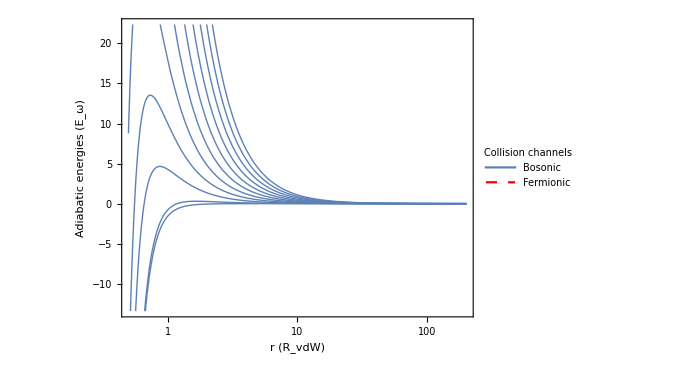

```mathematica
LogLinearPlot[{(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->Automatic,AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
N[abar]*4
```

1.91196

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[r_,A_,B_]=A Sqrt[r]BesselJ[1/4,1/(2 r^2)]+B Sqrt[r] BesselY[1/4,1/(2 r^2)];
```

```mathematica
ash[phi_]:=abar (1+Tan[phi])
```

```mathematica
as[y_,s_]:=abar(s+y(1+(1-s)^2)/(ⅈ+y(1-s)));
ap[y_,s_,k_]:=-2 abar1  (k abar)^2  (y+ⅈ(s-1))/(y s+ⅈ(s-2))
```

Table of short range solutions

```mathematica
Psi0[r_,A_,B_]:=Table[If[n1==n2,sol0[r,A,B],0] ,{n1,1,Nch},{n2,1,Nch}]
```

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,A_?NumericQ,B_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,Ro,Rprod},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],A,B].Inverse[Psi0[xt[[n0]],A,B]];
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=en Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
n++;
];
Ro=Rout[nf];
Rprod=Inverse[Rout[n0]];Do[Rprod=Rprod.Inverse[Rout[n]],{n,n0+1,nf-1}];
Clear[W,n,Rinv,h,h0,Qt];
If[cl==1,Clear[Rout]];
{Ro,Rprod}]
```

Subroutine calculating K matrix

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix

```mathematica
KMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
K];
```

Subroutine calculating K and T matrices

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix
T matrix

```mathematica
KCTMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R,W,T},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
Rprod=R[[2]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
W=Rprod.(J1+N1.K).Inverse[Id-ⅈ K];
R=ConjugateTranspose[W].W;
W=Inverse[Id-ⅈ K];
T=W.K/ Sqrt[en];
{T,K,Re[Tr[R]]}];
```

```mathematica
yy=0;ss=4.;
```

```mathematica
aS=as[yy,ss]
```

1.91196+0. ⅈ

```mathematica
aP=ap[yy,ss,Sqrt[en]]
```

(-0.348683+0. ⅈ) en

```mathematica
phi=φ/.Solve[aS==ash[φ],φ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.24905

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
```

energies

```mathematica
en0=0.0001;enf=100.;de=(Log[enf]-Log[en0])/50;
```

```mathematica
TabEn=Table[Exp[ee],{ee,Log[en0],Log[enf],de}]
```

{0.0001,0.000131826,0.00017378,0.000229087,0.000301995,0.000398107,0.000524807,0.000691831,0.000912011,0.00120226,0.00158489,0.0020893,0.00275423,0.00363078,0.0047863,0.00630957,0.00831764,0.0109648,0.0144544,0.0190546,0.0251189,0.0331131,0.0436516,0.057544,0.0758578,0.1,0.131826,0.17378,0.229087,0.301995,0.398107,0.524807,0.691831,0.912011,1.20226,1.58489,2.0893,2.75423,3.63078,4.7863,6.30957,8.31764,10.9648,14.4544,19.0546,25.1189,33.1131,43.6516,57.544,75.8578,100.}

loop

```mathematica
Elastic={};Inelastic={}; Sections={};
Print["Progress:"];
Print[ProgressIndicator[Dynamic[counter],{1,Length[TabEn]}]];
Do[en=TabEn[[i]];
counter=i;
(*Print["en = ",en];*)

xi=0.1;
(*Determines the final point of integration*)
xf=400;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)

totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,{en,a0}];

Clear[xt,QT];
,{i,1,Length[TabEn]}
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0465901,0.,1.08997×10^-6,0.,-5.16518×10^-8,0.,-3.05867×10^-11,0.,-2.52181×10^-14,0.,«11»},{0.,-0.0710489,0.,0.00004133,0.,2.24514×10^-8,0.,1.38843×10^-11,0.,1.16786×10^-14,«11»},{0.0000509158,0.,-0.0309527,0.,0.0000172131,0.,5.42713×10^-9,0.,3.48072×10^-12,0.,«11»},{0.,-0.0000421706,0.,-0.037791,0.,0.0000164317,0.,4.83554×10^-9,0.,3.08741×10^-12,«11»},{2.19142×10^-8,0.,-1.56331×10^-7,0.,-0.0700282,0.,0.0000252574,0.,7.43314×10^-9,0.,«11»},{0.,-7.57909×10^-9,0.,5.43614×10^-6,«3»,0.0000554707,0.,1.60012×10^-8,«11»},{3.50107×10^-12,0.,-1.32977×10^-11,0.,6.81376×10^-6,0.,-0.508825,0.,0.000156756,0.,«11»},{0.,-7.65201×10^-13,0.,2.6117×10^-10,0.,9.05547×10^-6,0.,-1.79481,0.,0.000535259,«11»},{3.00505×10^-16,0.,-8.87849×10^-16,0.,2.08749×10^-10,0.,0.0000163175,0.,-7.28487,0.,«11»},{0.,-4.7285×10^-17,0.,1.22503×10^-14,0.,1.91894×10^-10,0.,0.0000393189,0.,-33.397,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0397648,0.,0.0000433369,0.,-4.56359×10^-8,0.,-2.11482×10^-11,0.,-1.17669×10^-14,0.,«11»},{0.,0.47209,0.,-0.000132735,0.,-1.28201×10^-7,0.,-5.55878×10^-11,0.,-3.3657×10^-14,«11»},{0.0000112216,0.,-0.0419305,0.,0.0000190114,0.,5.46762×10^-9,0.,2.50788×10^-12,0.,«11»},{0.,0.000308297,0.,-0.035602,0.,0.000013867,0.,3.06918×10^-9,0.,1.44938×10^-12,«11»},{5.21803×10^-9,0.,-8.39473×10^-6,0.,-0.0523048,0.,0.000016226,0.,3.54001×10^-9,0.,«11»},{0.,6.78113×10^-8,0.,3.15785×10^-6,«3»,0.0000279583,0.,6.09114×10^-9,«11»},{8.474×10^-13,0.,-8.4606×10^-10,0.,5.68593×10^-6,0.,-0.263187,0.,0.0000644644,0.,«11»},{0.,7.24131×10^-12,0.,1.72127×10^-10,0.,6.88503×10^-6,0.,-0.787157,0.,0.00018378,«11»},{7.27935×10^-17,0.,-5.99128×10^-14,0.,1.91511×10^-10,0.,9.95168×10^-6,0.,-2.72544,0.,«11»},{0.,4.58814×10^-16,0.,8.50599×10^-15,0.,1.56964×10^-10,0.,0.0000192301,0.,-10.7013,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0516593,0.,0.000209719,0.,-7.9164×10^-8,0.,-3.77606×10^-11,0.,-1.38192×10^-14,0.,«11»},{0.,0.0679749,0.,5.62904×10^-6,0.,-1.82246×10^-8,0.,-6.03509×10^-12,0.,-2.59291×10^-15,«11»},{-0.000110429,0.,-0.0923044,0.,0.0000277923,0.,1.03492×10^-8,0.,3.4092×10^-12,0.,«11»},{0.,0.000035519,0.,-0.0399969,0.,0.0000138459,0.,2.61027×10^-9,0.,9.10457×10^-13,«11»},{-5.05357×10^-8,0.,-0.0000336931,0.,-0.0442231,0.,0.0000125817,0.,2.08248×10^-9,0.,«11»},{0.,9.70222×10^-9,0.,-1.16814×10^-6,«4»,0.,2.76614×10^-9,«11»},{-8.16159×10^-12,0.,-4.24804×10^-9,0.,4.2597×10^-6,0.,-0.150308,0.,0.0000306291,0.,«11»},{0.,1.1055×10^-12,0.,-7.57727×10^-11,0.,5.73505×10^-6,0.,-0.380332,0.,0.0000720243,«11»},{-6.93833×10^-16,0.,-3.25062×10^-13,0.,1.63775×10^-10,0.,7.11434×10^-6,0.,-1.12373,0.,«11»},{0.,7.23335×10^-17,0.,-4.02492×10^-15,0.,1.44932×10^-10,0.,0.0000109677,0.,-3.78614,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.0001,0.0000935116},{0.000131826,0.000113685},{0.00017378,0.000141221},{0.000229087,0.000182371},{0.000301995,0.00023644},{0.000398107,0.00030009},{0.000524807,0.000386993},{0.000691831,0.000502854},{0.000912011,0.000650583},{0.00120226,0.000849019},{0.00158489,0.0011083},{0.0020893,0.00144897},{0.00275423,0.00190003},{0.00363078,0.00249492},{0.0047863,0.00327847},{0.00630957,0.00431439},{0.00831764,0.00568165},{0.0109648,0.00748799},{0.0144544,0.00987125},{0.0190546,0.0130136},{0.0251189,0.0171508},{0.0331131,0.0225842},{0.0436516,0.0296984},{0.057544,0.0389738},{0.0758578,0.0509964},{0.1,0.0664591},{0.131826,0.0861397},{0.17378,0.110839},{0.229087,0.141256},{0.301995,0.177757},{0.398107,0.219998},{0.524807,0.266382},{0.691831,0.313352},{0.912011,0.354725},{1.20226,0.381599},{1.58489,0.384137},{2.0893,0.358115},{2.75423,0.32172},{3.63078,0.349902},{4.7863,0.619444},{6.30957,1.38522},{8.31764,2.72826},{10.9648,4.2916},{14.4544,5.88633},{19.0546,7.28154},{25.1189,8.3115},{33.1131,10.0571},{43.6516,11.7513},{57.544,13.2605},{75.8578,14.4588},{100.,19.8033}}

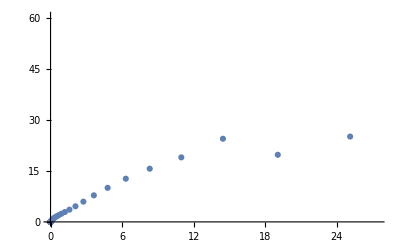

```mathematica
Inelastic
ListPlot[Elastic]
```

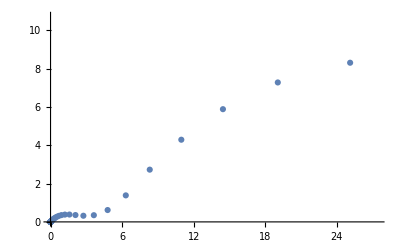

```mathematica
ListPlot[Inelastic]
```

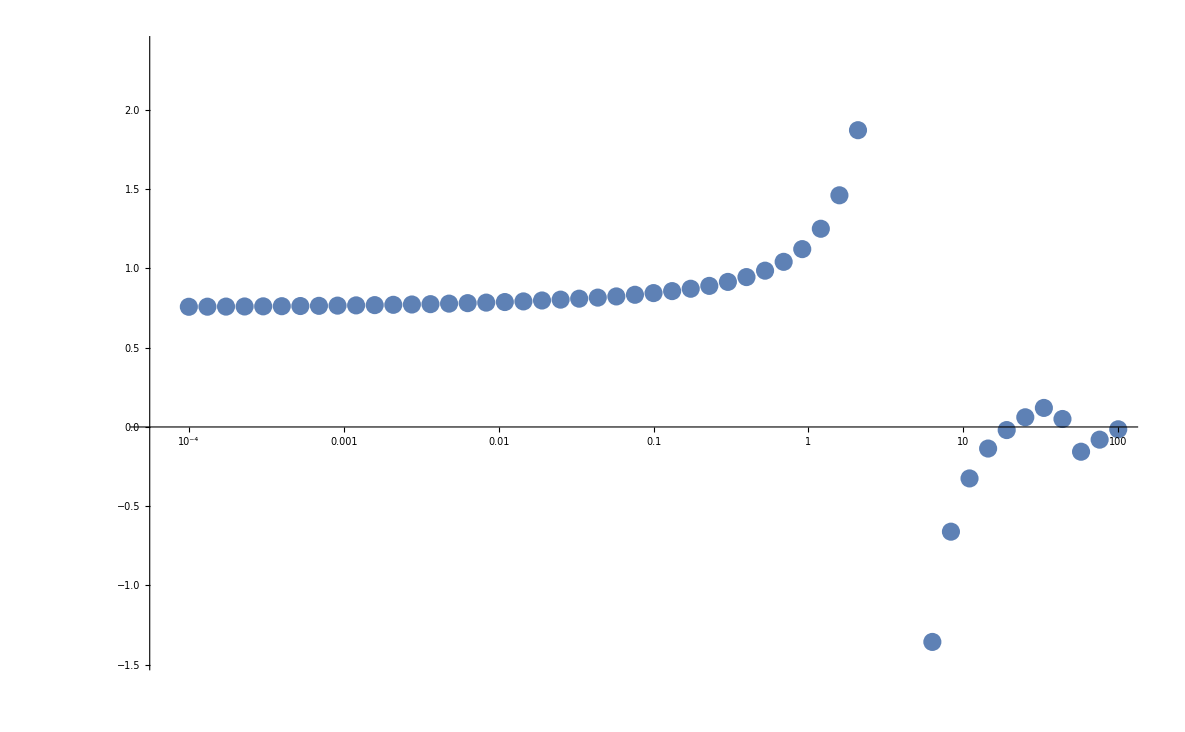

```mathematica
ListLogLinearPlot[Re[Sections]]
```

```mathematica
Re[Sections]
```

{{0.0001,0.758192},{0.000131826,0.758751},{0.00017378,0.759369},{0.000229087,0.760079},{0.000301995,0.760913},{0.000398107,0.761852},{0.000524807,0.762902},{0.000691831,0.764113},{0.000912011,0.765458},{0.00120226,0.766979},{0.00158489,0.768679},{0.0020893,0.770545},{0.00275423,0.772557},{0.00363078,0.774763},{0.0047863,0.778078},{0.00630957,0.781122},{0.00831764,0.784466},{0.0109648,0.788111},{0.0144544,0.792033},{0.0190546,0.797864},{0.0251189,0.803279},{0.0331131,0.809316},{0.0436516,0.816019},{0.057544,0.823479},{0.0758578,0.833881},{0.1,0.844521},{0.131826,0.857023},{0.17378,0.871926},{0.229087,0.889992},{0.301995,0.91508},{0.398107,0.9455},{0.524807,0.985967},{0.691831,1.04172},{0.912011,1.1219},{1.20226,1.25037},{1.58489,1.46145},{2.0893,1.8721},{2.75423,2.95162},{3.63078,11.8239},{4.7863,-3.83963},{6.30957,-1.35603},{8.31764,-0.660532},{10.9648,-0.324679},{14.4544,-0.136108},{19.0546,-0.0195552},{25.1189,0.0610449},{33.1131,0.120131},{43.6516,0.0503153},{57.544,-0.156178},{75.8578,-0.0800751},{100.,-0.0146771}}

Imports

```mathematica
imported = Import["Drop_3D_30_07.csv"];
imported=Sort[imported,#1[[1]]<#2[[1]]&];
scat=Transpose[imported][[1]];
scat = (1/aHOz)*scat;
scat=1/scat;

energies=Transpose[imported][[2]];
energies = Ωz * energies;

colored = Join[Transpose[imported], {Range[Length[scat]]}];
```

```mathematica
Export["Before_scat_colored.csv",Transpose[colored]]
```

Before_scat_colored.csv

Calculations

```mathematica
Elastic={};Inelastic={}; Sections={};Scattered={}; Sections1D={};
en = 0.0000001;
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[scat]}]];
Do[aS=scat[[i]];
k=i;
(*Print["as = ",aS];*)

xi=0.1;
(*Determines the final point of integration*)
xf=200;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
phi=φ/.Solve[aS==ash[φ],φ][[1]];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)
(*Print[a0];*)
totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,Re[a0]];
AppendTo[Sections1D,i];
AppendTo[Scattered,{aS,Re[a0]}];

Clear[xt,QT];
,{i,1,Length[scat]}
]
```

Progress:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00853059,0.,0.0298625,0.,0.112862,0.,0.768017,0.,6.13959,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09521,0.,18.2445,0.,131.117,«11»},{0.0000392273,0.,-32.7298,0.,75.9168,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274466,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.67439×10^-8,0.,0.00857357,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12268×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.54833×10^-12,0.,9.01189×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34438×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{7.36853×10^-16,0.,9.90601×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.2933×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00853039,0.,0.0298632,0.,0.112867,0.,0.768062,0.,6.14,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09521,0.,18.2445,0.,131.117,«11»},{0.0000392282,0.,-32.7298,0.,75.9168,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274466,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.67447×10^-8,0.,0.00857357,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12268×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.54859×10^-12,0.,9.01189×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34438×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{7.36903×10^-16,0.,9.90601×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.2933×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00853013,0.,0.029864,0.,0.112874,0.,0.768121,0.,6.14056,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09521,0.,18.2445,0.,131.117,«11»},{0.0000392293,0.,-32.7298,0.,75.9168,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274466,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.67457×10^-8,0.,0.00857357,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12268×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.54894×10^-12,0.,9.01189×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34438×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{7.36969×10^-16,0.,9.90601×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.2933×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

```mathematica
Spectral=Join[{aHOz/Sections},{energies/Ωz}];
Spectral1=Join[{aHOz/Sections},{energies/Ωz},{Sections1D}];
Spectral1=Transpose[Spectral1];
Spectral=Transpose[Spectral];
Spectral
```

```mathematica
Export["Spectral_02.csv",Spectral];
Export["Spectral_colored.csv",Spectral1];
```

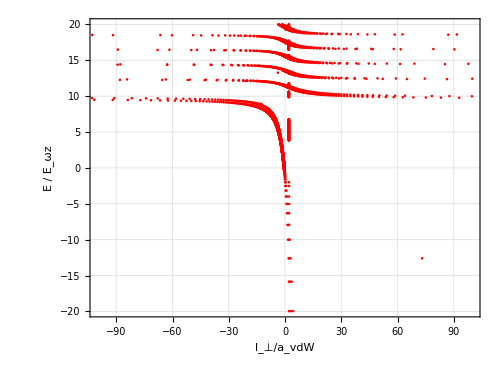

```mathematica
ListPlot[Re[Spectral],PlotRange->{{-100,100},All},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
Spectral
```

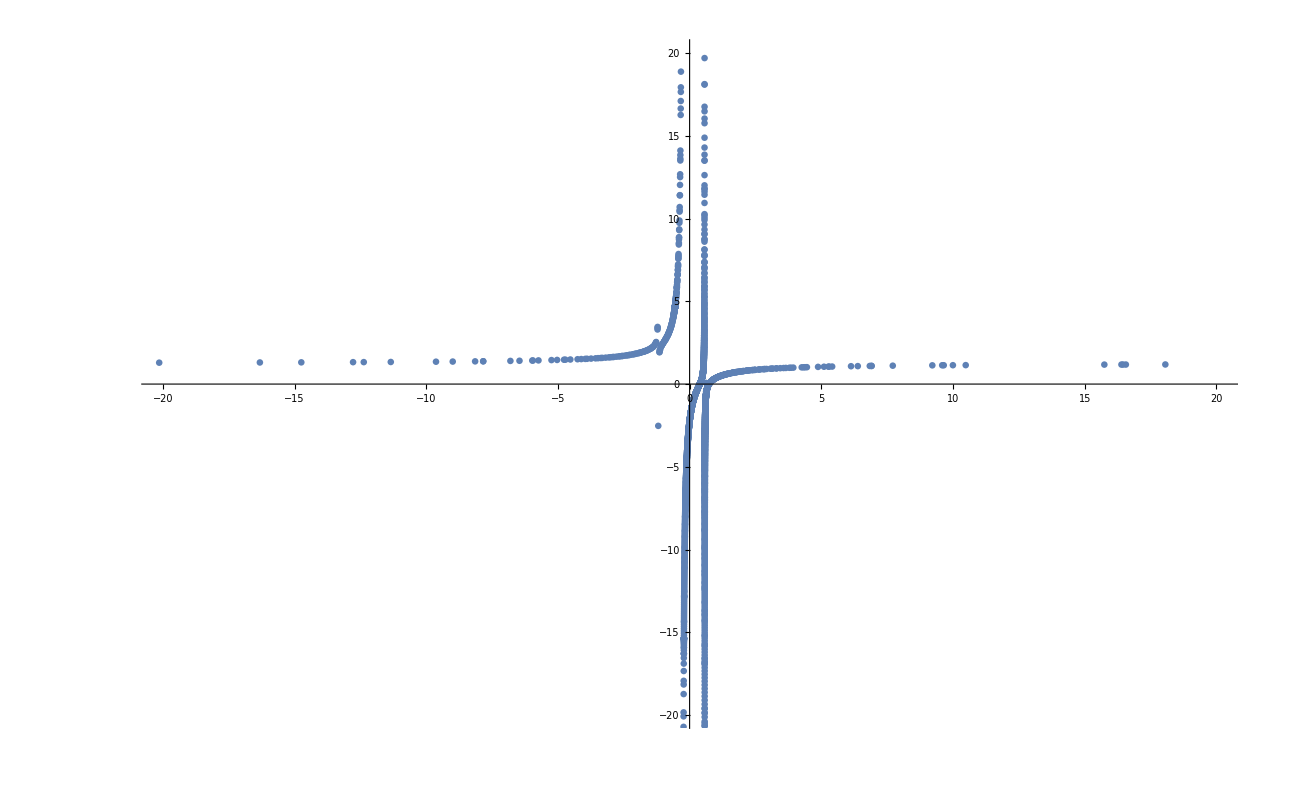

Scattered_02.csv

```mathematica
ListPlot[Re[Scattered], PlotRange->{{-20,20},{-20,20}}]
Export["Scattered_02.csv",Scattered]
```

```mathematica
Sections
```

{-2.23534,-2.23998,-2.24611,-2.25562,-2.25693,-2.26778,-2.27024,-2.27866,-2.28959,-2.30055,-2.31154,-2.32258,-2.33365,-2.34477,-2.35592,-2.36711,-2.36892,-2.37833,-2.3896,-2.40091,-2.41226,-2.41736,-2.42365,-2.4287,-2.43508,-2.44655,-2.45806,-2.46043,-2.46961,-2.48121,-2.49285,-2.50453,-2.51625,-2.52802,-2.53983,-2.55168,-2.56358,-2.56361,-2.57553,-2.58752,-2.59955,-2.61163,-2.61338,-2.61845,-2.62376,-2.63594,-2.64816,-2.66042,-2.67274,-2.67546,-2.6851,-2.69752,-2.70998,-2.72249,-2.73505,-2.74766,-2.76032,-2.77303,-2.78167,-2.78579,-2.79861,-2.81147,-2.82439,-2.82769,-2.83144,-2.83736,-2.85039,-2.86347,-2.8766,-2.88979,-2.90303,-2.91633,-2.92091,-2.92968,-2.94309,-2.95656,-2.97008,-2.98366,-2.9973,-3.011,-3.02476,-3.02792,-3.03857,-3.05245,-3.05991,-3.06639,-3.07583,-3.08039,-3.09445,-3.10857,-3.12275,-3.137,-3.15131,-3.16569,-3.18013,-3.19463,-3.2041,-3.2092,-3.22384,-3.23855,-3.25332,-3.26816,-3.28306,-3.29804,-3.30862,-3.31309,-3.31948,-3.3282,-3.34339,-3.35203,-3.35865,-3.37398,-3.38938,-3.40486,-3.4204,-3.43603,-3.45173,-3.4675,-3.48335,-3.49928,-3.51529,-3.53137,-3.53492,-3.54753,-3.56377,-3.5801,-3.5965,-3.61195,-3.61298,-3.62955,-3.63198,-3.6462,-3.66294,-3.66712,-3.67976,-3.69666,-3.71365,-3.73073,-3.74789,-3.76514,-3.78248,-3.79992,-3.81744,-3.83505,-3.85276,-3.87056,-3.88845,-3.90644,-3.92452,-3.92703,-3.9427,-3.94445,-3.96097,-3.97935,-3.99782,-4.00909,-4.0164,-4.03045,-4.03507,-4.05385,-4.07273,-4.09171,-4.1108,-4.12999,-4.14929,-4.1687,-4.18821,-4.20784,-4.22758,-4.24742,-4.26738,-4.28746,-4.30765,-4.32634,-4.32795,-4.34837,-4.36891,-4.38957,-4.39984,-4.41035,-4.43125,-4.45227,-4.45462,-4.45518,-4.47342,-4.49469,-4.51609,-4.53762,-4.55927,-4.58105,-4.60297,-4.62502,-4.6472,-4.66952,-4.69197,-4.71456,-4.73729,-4.76016,-4.77012,-4.78318,-4.80633,-4.82963,-4.85308,-4.87668,-4.90042,-4.92432,-4.94836,-4.95702,-4.97256,-4.98192,-4.99184,-4.99692,-5.02144,-5.04611,-5.07094,-5.09594,-5.1211,-5.14642,-5.17191,-5.19758,-5.22341,-5.24941,-5.27559,-5.29289,-5.30195,-5.32848,-5.35519,-5.38209,-5.40917,-5.43643,-5.46389,-5.49153,-5.51937,-5.5474,-5.56235,-5.57562,-5.60405,-5.63267,-5.65073,-5.6615,-5.69054,-5.6911,-5.71709,-5.71978,-5.74923,-5.7789,-5.80878,-5.83887,-5.86919,-5.89973,-5.91867,-5.93049,-5.96148,-5.99271,-6.02416,-6.05585,-6.08778,-6.11995,-6.15236,-6.18502,-6.21793,-6.25109,-6.28451,-6.30692,-6.31819,-6.3241,-6.35213,-6.38633,-6.42081,-6.45555,-6.48014,-6.49057,-6.52587,-6.56145,-6.59732,-6.63347,-6.66992,-6.67618,-6.68228,-6.70667,-6.74371,-6.78106,-6.81872,-6.85669,-6.89497,-6.93357,-6.9725,-7.01176,-7.05135,-7.08751,-7.09127,-7.13154,-7.17215,-7.21312,-7.24634,-7.25444,-7.29612,-7.33816,-7.38057,-7.42336,-7.46653,-7.51008,-7.55403,-7.59837,-7.63625,-7.64311,-7.68825,-7.73382,-7.77979,-7.8262,-7.87303,-7.9203,-7.96802,-7.98163,-8.01618,-8.02754,-8.0648,-8.11388,-8.16343,-8.21346,-8.26397,-8.31497,-8.36647,-8.41847,-8.47036,-8.47099,-8.52402,-8.57759,-8.63169,-8.68634,-8.74154,-8.7973,-8.85363,-8.86358,-8.91055,-8.96805,-9.02615,-9.08485,-9.14418,-9.20413,-9.21506,-9.26472,-9.32596,-9.38785,-9.45042,-9.51366,-9.5776,-9.64224,-9.7076,-9.77368,-9.8405,-9.8649,-9.90808,-9.97642,-10.0455,-10.1155,-10.1338,-10.1862,-10.2577,-10.3301,-10.4033,-10.4774,-10.5037,-10.5524,-10.6282,-10.705,-10.7647,-10.7827,-10.8614,-10.941,-11.0216,-11.1032,-11.1045,-11.1858,-11.2695,-11.3542,-11.44,-11.5269,-11.6149,-11.7041,-11.7944,-11.8859,-11.9787,-12.0727,-12.1679,-12.2644,-12.3623,-12.4615,-12.5284,-12.562,-12.664,-12.7674,-12.8104,-12.8227,-12.8722,-12.8749,-12.9786,-13.0865,-13.1959,-13.3069,-13.4196,-13.5339,-13.6499,-13.7677,-13.8872,-14.0086,-14.1318,-14.2569,-14.3472,-14.384,-14.5131,-14.6442,-14.7774,-14.9128,-15.0503,-15.1902,-15.3323,-15.3502,-15.3525,-15.3555,-15.3591,-15.3638,-15.3696,-15.377,-15.3863,-15.398,-15.4127,-15.4314,-15.4548,-15.4845,-15.522,-15.5694,-15.6294,-15.7056,-15.8025,-15.9209,-15.926,-16.0838,-16.278,-16.2866,-16.2984,-16.5484,-16.8888,-17.3356,-17.929,-18.1491,-18.73,-19.8349,-20.0761,-20.7095,-21.4056,-22.1968,-22.9965,-23.7372,-27.4299,-29.3482,-30.6079,-32.9503,-33.9244,-34.3429,-38.5485,-47.7707,-49.6361,-73.9254,-88.6291,-93.7034,-94.8912,-114.006,-154.227,572.454,496.019,144.216,134.869,124.196,91.5369,59.7858,58.652,49.6899,40.7305,38.8087,31.816,31.1164,30.2081,28.673,24.5417,22.8345,21.798,21.7944,18.8762,17.9283,17.6517,17.1017,16.6463,16.2593,14.1082,13.8364,13.6165,13.508,12.6746,12.5044,12.0327,11.4142,11.3966,10.6948,10.5101,10.4206,9.88052,9.74216,9.34687,9.29822,8.87604,8.84115,8.7415,8.52173,8.43144,7.85782,7.757,7.69521,7.59637,7.56866,7.23072,7.15702,7.09429,6.91699,6.8773,6.6537,6.6,6.59427,6.31218,6.27544,6.1936,6.14167,5.98459,5.87034,5.86304,5.84476,5.78799,5.78216,5.60024,5.53418,5.50646,5.5049,5.43098,5.39808,5.30013,5.29099,5.24786,5.19013,5.18693,5.15513,5.13884,5.12479,5.06015,5.05471,5.0313,5.01494,5.00274,5.00105,4.98491,4.97407,4.95999,4.94205,4.93529,4.93447,4.92739,4.90192,4.89897,4.89292,4.89223,4.88159,4.87271,4.87154,4.86502,4.85684,4.85128,4.85025,4.83971,4.83329,4.83138,4.83073,4.82984,4.80233,4.78097,4.76468,4.75188,4.74154,4.73303,4.72589,4.72226,4.72088,4.7198,4.71954,4.71825,4.717,4.71579,4.71462,4.71454,4.71348,4.71237,4.71128,4.71023,4.70995,4.70919,4.70818,4.70718,4.70621,4.7059,4.70525,4.70431,4.70338,4.70246,4.70229,4.70156,4.70066,4.69978,4.69905,4.6989,4.69803,4.69717,4.69631,4.69612,4.69546,4.69461,4.69377,4.69293,4.69209,4.69125,4.69041,4.69024,4.68799,4.68562,4.6831,4.68043,4.67757,4.6745,4.67121,4.66764,4.66376,4.65953,4.65487,4.64973,4.64401,4.63759,4.63624,4.63566,4.63509,4.63454,4.634,4.63347,4.63296,4.63245,4.63195,4.63146,4.63098,4.63051,4.63033,4.63005,4.62959,4.62914,4.6287,4.62826,4.62783,4.6274,4.62698,4.62657,4.62616,4.62576,4.62536,4.62496,4.62457,4.62419,4.6238,4.62343,4.62305,4.62268,4.62231,4.62204,4.62195,4.62159,4.62123,4.62087,4.62052,4.62017,4.61982,4.61948,4.61914,4.6188,4.61846,4.61812,4.61779,4.61746,4.61713,4.6168,4.61648,4.61522,4.61384,4.61311,4.61249,4.61237,4.61094,4.6108,4.60912,4.60732,4.60536,4.60458,4.6044,4.60324,4.60136,4.60092,4.59837,4.59721,4.59554,4.59418,4.59239,4.58883,4.58854,4.5882,4.58478,4.58287,4.58199,4.58013,4.57821,4.57471,4.57244,4.56831,4.56724,4.56701,4.56678,4.56654,4.56631,4.56607,4.56584,4.56568,4.5656,4.56537,4.56513,4.5649,4.56466,4.56443,4.5642,4.56396,4.56373,4.56349,4.56326,4.56303,4.56279,4.56256,4.56233,4.56209,4.56186,4.56162,4.56139,4.56116,4.56092,4.56069,4.56061,4.56046,4.56023,4.55999,4.55976,4.55953,4.55929,4.55906,4.55883,4.5586,4.55836,4.55813,4.5579,4.55767,4.55743,4.5572,4.55697,4.55674,4.55651,4.55627,4.55604,4.55581,4.55558,4.55535,4.55511,4.55488,4.55465,4.55442,4.55419,4.55395,4.55372,4.55349,4.55326,4.55325,4.55303,4.5528,4.55257,4.55233,4.5521,4.55187,4.55164,4.55141,4.55118,4.55116,4.55095,4.55072,4.55048,4.55025,4.55016,4.55002,4.54979,4.54956,4.54933,4.5491,4.54902,4.54887,4.54864,4.54841,4.54818,4.54795,4.54771,4.54748,4.54725,4.54702,4.54679,4.54656,4.54633,4.5461,4.54587,4.54564,4.54541,4.54518,4.54495,4.54472,4.54449,4.54426,4.54403,4.5438,4.54356,4.54333,4.5431,4.54287,4.54264,4.54241,4.54218,4.54195,4.54172,4.54149,4.54126,4.54103,4.5408,4.54057,4.54034,4.54011,4.53988,4.53965,4.53942,4.53929,4.53919,4.53896,4.53873,4.5385,4.53827,4.53804,4.53781,4.53758,4.53735,4.53712,4.53689,4.53666,4.53643,4.5362,4.53597,4.53574,4.53551,4.53528,4.53505,4.53482,4.53459,4.53436,4.53413,4.5339,4.53367,4.53344,4.53321,4.53298,4.53275,4.53252,4.53229,4.53206,4.53183,4.5316,4.53137,4.53114,4.53091,4.53068,4.53049,4.53045,4.53021,4.52998,4.52975,4.52952,4.52949,4.52929,4.52906,4.52883,4.5286,4.52837,4.52814,4.52791,4.52768,4.52745,4.52722,4.52699,4.52676,4.52653,4.5263,4.52608,4.52607,4.52584,4.52561,4.52538,4.52515,4.52492,4.52468,4.52445,4.52422,4.52399,4.52393,4.50491,4.50333,4.49953,4.49652,4.47451,4.47065,4.46109,4.45754,4.43505,4.4321,4.43114,4.42619,4.42344,4.41157,4.41109,4.40518,4.39927,4.37833,4.3664,4.35707,4.34836,4.34578,4.33801,4.3343,4.30151,4.26404,4.262,4.26149,4.23984,4.23002,4.21478,4.15641,4.13939,4.11986,4.10443,4.08174,4.03238,4.00887,3.98631,3.97825,3.90132,3.89978,3.89472,3.82342,3.81593,3.74998,3.70648,3.67489,3.66404,3.64037,3.60369,3.57979,3.51209,3.50629,3.46787,3.4596,3.45281,3.35363,3.32595,3.31977,3.30258,3.24397,3.20755,3.18514,3.15082,3.14592,3.07945,3.06829,3.05581,3.05075,2.99761,2.98646,2.93223,2.92514,2.87292,2.85797,2.83289,2.81196,2.80865,2.72281,2.70477,2.69435,2.68507,2.68464,2.59005,2.57674,2.56087,2.54092,2.53872,2.4532,2.45211,2.42976,2.37978,2.3624,2.30681,2.28597,2.26752,2.14563,2.06395,2.0536,1.94262,1.92022,-2.52483,26.1573,3.45238,3.38721,3.29808,2.54039,2.50963,2.44325,2.42338,2.39191,2.30468,2.2712,2.25867,2.24227,2.20669,2.1777,2.14312,2.14091,2.1266,2.0866,2.08022,2.0504,2.03996,2.03315,1.99605,1.98927,1.96908,1.95293,1.95111,1.91964,1.90433,1.89486,1.87636,1.87456,1.8485,1.8278,1.82571,1.80691,1.8024,1.78133,1.76046,1.75764,1.74164,1.73511,1.7173,1.6984,1.69266,1.6798,1.67184,1.65591,1.63904,1.63204,1.6209,1.61199,1.59676,1.58201,1.5752,1.56455,1.55513,1.53958,1.52704,1.52167,1.51047,1.50091,1.48412,1.47389,1.4711,1.45839,1.44904,1.43021,1.42318,1.42237,1.40813,1.39929,1.37768,1.37766,1.37232,1.35951,1.35145,1.33431,1.32639,1.32361,1.31237,1.30536,1.29295,1.27622,1.27611,1.26659,1.18427,1.17923,1.17883,1.17861,1.17608,1.14434,1.13975,1.13621,1.13558,1.1314,1.11076,1.0962,1.09604,1.09474,1.08472,1.07842,1.05784,1.05413,1.05307,1.04722,1.03868,1.02043,1.01709,1.01429,1.01076,0.993227,0.987944,0.983888,0.975154,0.969034,0.959733,0.948279,0.948139,0.936654,0.932393,0.92783,0.91312,0.905869,0.90377,0.898725,0.887085,0.880112,0.878767,0.861306,0.859633,0.855076,0.846735,0.845022,0.830718,0.824339,0.815804,0.81183,0.806999,0.80672,0.787768,0.783883,0.779138,0.772217,0.766983,0.761336,0.751538,0.746896,0.739326,0.728812,0.727465,0.717824,0.715597,0.715056,0.696803,0.688109,0.685524,0.683571,0.679892,0.676238,0.656103,0.652397,0.648858,0.644371,0.642292,0.636377,0.621489,0.617038,0.609654,0.608984,0.59905,0.598068,0.590805,0.579446,0.573679,0.570439,0.561157,0.560302,0.555735,0.543182,0.538404,0.531154,0.529938,0.525507,0.512282,0.508116,0.503107,0.499671,0.491739,0.490996,0.474134,0.469459,0.468622,0.467734,0.457516,0.452131,0.441132,0.439261,0.432231,0.424969,0.424688,0.412267,0.409032,0.409018,0.396543,0.393267,0.380411,0.37873,0.377708,0.372082,0.362331,0.360612,0.348312,0.347129,0.335725,0.332091,0.331511,0.324381,0.317734,0.317212,0.302483,0.290563,0.290492,0.287898,0.287793,0.286952,0.27345,0.259133,0.255924,0.250794,0.248963,0.244942,0.244871,0.230872,0.224607,0.216917,0.213332,0.206874,0.203075,0.198607,0.192968,0.189343,0.175721,0.175381,0.164227,0.16222,0.161014,0.151878,0.148897,0.137976,0.130184,0.127741,0.121617,0.120389,0.1086,0.103913,0.0974087,0.0955432,0.0953775,0.0825357,0.0765205,0.0695934,0.0620339,0.0576451,0.0567202,0.0557695,0.0439167,0.031753,0.0311823,0.0281438,0.0185162,0.017174,0.00691723,0.0059174,-0.00629642,-0.00661525,-0.0137477,-0.0190828,-0.0239911,-0.0314862,-0.0413051,-0.0425699,-0.0438265,-0.0561047,-0.0599638,-0.0658557,-0.0683216,-0.076902,-0.0804781,-0.092575,-0.0926549,-0.104613,-0.106882,-0.108426,-0.113107,-0.116594,-0.128517,-0.140383,-0.143306,-0.149941,-0.151708,-0.152195,-0.154492,-0.163952,-0.175655,-0.187306,-0.187427,-0.1945,-0.195713,-0.198904,-0.202789,-0.21045,-0.221947,-0.225593,-0.233394,-0.240458,-0.244793,-0.24623,-0.251778,-0.256144,-0.264472,-0.267449,-0.278708,-0.285972,-0.289923,-0.298507,-0.301096,-0.301485,-0.304108,-0.312226,-0.323317,-0.332303,-0.334368,-0.344559,-0.345381,-0.35138,-0.351962,-0.356359,-0.367303,-0.378214,-0.37953,-0.385906,-0.389095,-0.399948,-0.403316,-0.404954,-0.410775,-0.421581,-0.427793,-0.428275,-0.432367,-0.443137,-0.453897,-0.45576,-0.459463,-0.464651,-0.471885,-0.475405,-0.477369,-0.486168,-0.49695,-0.507761,-0.509817,-0.515506,-0.517202,-0.518619,-0.528952,-0.529544,-0.540564,-0.551719,-0.563066,-0.565579,-0.567251,-0.574691,-0.575306,-0.585149,-0.586729,-0.599408,-0.613142,-0.624221,-0.628777,-0.641777,-0.648341,-0.662153,-0.676778,-0.678243,-0.754998,0.0690788,-0.452582,-0.559225,-0.611786,-0.61777,-0.637188,-0.640357,-0.641678,-0.655056,-0.669767,-0.673103,-0.682852,-0.694985,-0.704904,-0.706509,-0.713981,-0.716846,-0.717618,-0.728429,-0.731357,-0.739019,-0.749437,-0.75972,-0.766763,-0.769893,-0.772859,-0.778427,-0.779974,-0.784916,-0.789979,-0.799919,-0.809802,-0.819636,-0.826461,-0.829425,-0.830457,-0.838292,-0.838302,-0.839176,-0.848892,-0.858576,-0.868231,-0.87786,-0.886288,-0.887465,-0.888534,-0.892596,-0.897048,-0.898193,-0.90661,-0.916154,-0.925679,-0.935189,-0.944684,-0.946922,-0.947683,-0.948261,-0.954164,-0.958693,-0.963632,-0.973087,-0.982531,-0.991964,-1.00139,-1.00559,-1.00822,-1.00869,-1.0108,-1.02007,-1.02021,-1.02961,-1.039,-1.04839,-1.05776,-1.06482,-1.06714,-1.07038,-1.07181,-1.07651,-1.08252,-1.08587,-1.09523,-1.10459,-1.11395,-1.1233,-1.12616,-1.13265,-1.13435,-1.13646,-1.142,-1.1462,-1.15135,-1.1607,-1.17004,-1.17939,-1.18874,-1.18984,-1.19809,-1.20032,-1.20282,-1.20744,-1.21126,-1.2168,-1.22615,-1.23551,-1.24487,-1.25423,-1.2561,-1.2636,-1.26851,-1.27107,-1.27297,-1.27783,-1.28235,-1.29173,-1.30112,-1.31051,-1.31991,-1.32519,-1.32931,-1.33872,-1.33913,-1.34138,-1.34608,-1.34814,-1.35756,-1.36699,-1.37643,-1.38588,-1.39533,-1.39739,-1.4048,-1.41239,-1.41394,-1.41427,-1.41616,-1.42375,-1.43325,-1.44275,-1.45226,-1.46178,-1.47132,-1.47303,-1.48086,-1.48824,-1.48857,-1.48898,-1.49042,-1.49999,-1.50957,-1.51916,-1.52877,-1.53839,-1.54802,-1.55244,-1.55767,-1.56252,-1.56672,-1.56733,-1.56794,-1.577,-1.58669,-1.59639,-1.60611,-1.61584,-1.62559,-1.63536,-1.63603,-1.63918,-1.64514,-1.64742,-1.6508,-1.65494,-1.66475,-1.67459,-1.68444,-1.6943,-1.70419,-1.71409,-1.71846,-1.72402,-1.72425,-1.73136,-1.73396,-1.73752,-1.74392,-1.7539,-1.7639,-1.77392,-1.78396,-1.79402,-1.80059,-1.8041,-1.81421,-1.8176,-1.81884,-1.82433,-1.82848,-1.83448,-1.84465,-1.85484,-1.86506,-1.87529,-1.88555,-1.88585,-1.89584,-1.90615,-1.91023,-1.91648,-1.91668,-1.92412,-1.92684,-1.93722,-1.94763,-1.95806,-1.96852,-1.97452,-1.97901,-1.98952,-2.00006,-2.00591,-2.01062,-2.02122,-2.02215,-2.02495,-2.03184,-2.04249,-2.05316,-2.06387,-2.06694,-2.0746,-2.08537,-2.09616,-2.10632,-2.10699,-2.11784,-2.12872,-2.13153,-2.13479,-2.13964,-2.15059,-2.16157,-2.16347,-2.17258,-2.18362,-2.1947,-2.2058,-2.21195,-2.21695,-2.22812,-2.23933,-2.24451,-2.25057,-2.25552,-2.26185,-2.26453,-2.27317,-2.28452,-2.2959,-2.30732,-2.31878,-2.32338,-2.33027,-2.34181,-2.35338,-2.36465,-2.36498,-2.37057,-2.37663,-2.38538,-2.38831,-2.40004,-2.4118,-2.4236,-2.43545,-2.44124,-2.44733,-2.45926,-2.47122,-2.48213,-2.48323,-2.49528,-2.50737,-2.51951,-2.52564,-2.53169,-2.54391,-2.55618,-2.56626,-2.5685,-2.58085,-2.59326,-2.59978,-2.60571,-2.6182,-2.63075,-2.64334,-2.65597,-2.6593,-2.66866,-2.67777,-2.6814,-2.69418,-2.6993,-2.70701,-2.7199,-2.7242,-2.73283,-2.74582,-2.75886,-2.77194,-2.77413,-2.77741,-2.78509,-2.79828,-2.81153,-2.82483,-2.83819,-2.84134,-2.84355,-2.8516,-2.85618,-2.86506,-2.87859,-2.89217,-2.89523,-2.9058,-2.9195,-2.93325,-2.9364,-2.94706,-2.96093,-2.97486,-2.98885,-2.99351,-2.99658,-3.0029,-3.01701,-3.02328,-3.02514,-3.03118,-3.04542,-3.05972,-3.07408,-3.08851,-3.103,-3.11756,-3.13218,-3.14645,-3.14687,-3.15715,-3.15907,-3.16163,-3.17646,-3.19135,-3.20632,-3.22135,-3.22512,-3.23646,-3.25163,-3.26688,-3.2822,-3.29759,-3.3035,-3.30698,-3.31306,-3.32861,-3.33385,-3.34422,-3.35992,-3.37569,-3.39154,-3.40746,-3.42347,-3.43956,-3.44673,-3.45572,-3.45761,-3.47197,-3.47956,-3.4883,-3.50471,-3.52121,-3.52547,-3.53779,-3.55446,-3.57121,-3.58805,-3.60498,-3.62199,-3.62262,-3.6391,-3.6563,-3.66585,-3.67359,-3.69097,-3.69397,-3.70844,-3.72601,-3.73426,-3.74367,-3.76143,-3.77928,-3.79723,-3.79994,-3.81529,-3.83344,-3.85169,-3.8678,-3.87004,-3.8885,-3.90706,-3.92573,-3.9445,-3.96293,-3.96338,-3.97187,-3.98236,-3.99124,-4.00146,-4.02066,-4.03998,-4.05941,-4.07896,-4.08776,-4.09861,-4.11839,-4.13828,-4.15829,-4.17842,-4.1985,-4.19867,-4.2148,-4.21905,-4.23954,-4.26017,-4.28091,-4.28691,-4.30179,-4.32279,-4.32856,-4.34393,-4.36519,-4.38659,-4.40813,-4.42409,-4.42979,-4.4516,-4.47355,-4.49395,-4.49563,-4.51786,-4.54023,-4.56274,-4.5854,-4.59365,-4.60821,-4.63117,-4.64748,-4.65428,-4.67083,-4.67755,-4.70097,-4.72454,-4.74827,-4.77217,-4.79622,-4.80545,-4.82044,-4.84482,-4.86937,-4.88727,-4.89409,-4.91898,-4.94221,-4.94405,-4.96929,-4.9947,-5.0203,-5.04607,-5.06471,-5.07203,-5.09818,-5.12451,-5.15104,-5.15575,-5.17775,-5.20466,-5.21472,-5.23177,-5.24247,-5.25907,-5.28658,-5.31429,-5.3422,-5.37033,-5.39867,-5.42722,-5.45598,-5.48497,-5.51418,-5.54361,-5.55309,-5.55368,-5.57327,-5.5769,-5.58266,-5.60316,-5.63328,-5.66364,-5.69424,-5.72508,-5.75617,-5.78709,-5.7875,-5.81909,-5.85093,-5.88303,-5.91539,-5.94801,-5.95213,-5.9809,-5.99965,-6.00822,-6.01407,-6.04751,-6.08122,-6.11523,-6.13531,-6.14951,-6.18409,-6.21896,-6.25413,-6.2896,-6.32538,-6.3313,-6.36147,-6.37667,-6.39787,-6.43459,-6.47164,-6.4768,-6.50901,-6.53544,-6.54672,-6.58476,-6.62315,-6.66188,-6.70096,-6.7404,-6.78021,-6.82038,-6.83951,-6.86092,-6.8615,-6.90184,-6.94314,-6.97695,-6.98484,-7.02692,-7.02886,-7.06941,-7.11231,-7.15415,-7.15561,-7.19934,-7.24349,-7.28807,-7.3331,-7.37856,-7.42116,-7.42448,-7.47086,-7.5177,-7.56502,-7.61282,-7.66111,-7.67583,-7.70989,-7.71063,-7.75634,-7.75918,-7.80898,-7.8593,-7.89142,-7.91014,-7.96153,-8.01346,-8.06595,-8.07523,-8.11901,-8.17263,-8.22684,-8.28165,-8.33706,-8.39308,-8.44547,-8.44973,-8.50701,-8.56494,-8.62352,-8.68278,-8.74271,-8.78613,-8.80334,-8.81728,-8.85079,-8.86468,-8.92673,-8.98951,-9.05304,-9.11733,-9.18238,-9.24823,-9.31487,-9.37758,-9.38233,-9.45062,-9.51976,-9.58976,-9.66064,-9.73242,-9.78635,-9.80511,-9.87873,-9.89623,-9.93246,-9.95331,-10.0288,-10.1054,-10.1829,-10.2615,-10.2716,-10.3411,-10.4218,-10.5036,-10.5312,-10.5865,-10.6705,-10.7557,-10.8421,-10.9297,-10.9386,-11.0185,-11.1086,-11.2,-11.2928,-11.3121,-11.3868,-11.4823,-11.5213,-11.5792,-11.6775,-11.7773,-11.8786,-11.9814,-11.9979,-12.0859,-12.1919,-12.2706,-12.2996,-12.3945,-12.409,-12.5202,-12.6331,-12.7479,-12.8645,-12.983,-13.1036,-13.1827,-13.2261,-13.3507,-13.4774,-13.6063,-13.6899,-13.7374,-13.8708,-13.9277,-14.0065,-14.1447,-14.2853,-14.2949,-14.4285,-14.5743,-14.7228,-14.8741,-15.0282,-15.1853,-15.1939,-15.3453,-15.5085,-15.6748,-15.773,-15.8444,-16.0174,-16.1939,-16.374,-16.5578,-16.5851,-16.7455,-16.831,-16.8835,-16.937,-17.1327,-17.3325,-17.5367,-17.7454,-17.9587,-18.1768,-18.3998,-18.628,-18.8615,-19.1004,-19.3451,-19.5957,-19.6027,-19.8523,-19.8819,-20.1153,-20.3849,-20.4825,-20.622,-20.6614,-20.9449,-21.2358,-21.5343,-21.7952,-21.8408,-22.1557,-22.4791,-22.8116,-23.1535,-23.5051,-23.867,-24.2395,-24.6231,-25.0185,-25.426,-25.8463,-25.8507,-26.28,-26.504,-26.7277,-26.7617,-27.1902,-27.6681,-28.1623,-28.6351,-28.6736,-29.2029,-29.7512,-30.3195,-30.8333,-30.9089,-31.5207,-32.1562,-32.8167,-33.5037,-34.219,-34.9642,-35.7413,-36.5524,-37.1309,-37.3998,-37.8855,-38.2859,-38.5867,-39.2136,-40.1857,-41.2055,-42.2768,-43.4033,-43.5483,-43.5671,-43.5908,-43.6207,-43.6584,-43.706,-43.766,-43.8418,-43.9376,-44.0588,-44.2122,-44.4069,-44.6544,-44.9697,-45.373,-45.8907,-46.5591,-47.4279,-48.5675,-50.0803,-50.8266,-52.1204,-52.4915,-54.9313,-58.9202,-62.1734,-64.8256,-69.1798,-70.7533,-74.1388,-90.3986,-124.551,-174.807,-193.259,-220.329,-235.696,-336.506,-530.736,2112.81,172.108,157.898,132.044,116.986,96.456,95.228,73.5693,59.2297,49.7073,47.9712,44.3381,44.1784,39.2784,35.6395,31.4946,29.7882,29.315,28.625,25.4126,24.7832,23.0079,21.2548,21.1511,21.1028,19.6952,18.1203,18.0937,16.7551,16.4784,16.04,15.7607,14.8854,14.2892,13.8576,13.5094,13.4994,12.6239,12.0066,11.8019,11.7992,11.6292,11.44,10.9422,10.2662,10.1935,10.0498,9.9137,9.64137,9.33401,9.07405,9.05545,8.75232,8.74029,8.60412,8.13028,8.12083,7.8092,7.75681,7.75101,7.37373,7.36255,7.34044,7.05164,7.0509,6.95426,6.71456,6.68909,6.45308,6.42261,6.30472,6.15973,6.13665,5.93975,5.90247,5.89144,5.76467,5.67881,5.66167,5.4937,5.43648,5.30824,5.2575,5.2485,5.10209,5.04205,4.91715,4.88541,4.88498,4.77752,4.75516,4.69647,4.57805,4.56348,4.55286,4.44533,4.39089,4.28104,4.27578,4.2546,4.16665,4.11848,4.01856,4.01686,3.98497,3.91437,3.90366,3.87387,3.78476,3.78234,3.73978,3.68467,3.65279,3.57505,3.5687,3.51559,3.4744,3.45181,3.38577,3.37307,3.30961,3.28099,3.26812,3.21527,3.21396,3.19306,3.11948,3.1023,3.09941,3.05723,3.02671,2.94378,2.94325,2.93652,2.91357,2.87234,2.79961,2.78213,2.78135,2.77927,2.72855,2.66597,2.66556,2.65917,2.63784,2.62614,2.59415,2.54588,2.54046,2.50254,2.48265,2.46811,2.44047,2.42334,2.37527,2.34955,2.34777,2.3421,2.31336,2.25521,2.25004,2.23769,2.22235,2.22061,2.20977,2.16366,2.14163,2.13189,2.11194,2.10039,2.0824,2.0339,2.03154,2.01932,2.00578,1.98643,1.93614,1.93339,1.93148,1.9314,1.87813,1.86484,1.84777,1.84523,1.83387,1.79982,1.77497,1.76804,1.75841,1.74063,1.73802,1.69188,1.67919,1.67533,1.65139,1.6231,1.61897,1.59566,1.58226,1.56953,1.56579,1.54904,1.51911,1.5183,1.48353,1.48186,1.46925,1.44544,1.4222,1.41721,1.40513,1.40434,1.37704,1.37441,1.35488,1.33362,1.32796,1.3058,1.2947,1.29185,1.25416,1.2516,1.24108,1.23943,1.2365,1.2128,1.18275,1.18014,1.17534,1.17513,1.16331,1.13915,1.12549,1.11354,1.11274,1.10416,1.07241,1.07029,1.05212,1.04636,1.03749,1.0208,1.01518,1.00569,0.993137,0.981058,0.974852,0.970557,0.944913,0.944445,0.935673,0.921581,0.917498,0.915832,0.887566,0.879619,0.875715,0.873788,0.860074,0.85555,0.833321,0.827097,0.824876,0.80884,0.807271,0.795102,0.781893,0.781434,0.771355,0.757156,0.743687,0.736733,0.736047,0.733032,0.718971,0.709494,0.692929,0.686519,0.680133,0.678291,0.667649,0.664083,0.649966,0.642163,0.621744,0.62074,0.618066,0.61732,0.60779,0.599794,0.579307,0.567917,0.566351,0.566325,0.559261,0.557382,0.53964,0.525603,0.520429,0.519382,0.511959,0.501612,0.497984,0.4855,0.483176,0.471657,0.465107,0.458572,0.447393,0.446,0.439774,0.430021,0.424686,0.412979,0.407062,0.406091,0.396257,0.382655,0.379843,0.378413,0.368643,0.363727,0.354441,0.347899,0.332778,0.33235,0.330701,0.326524,0.317069,0.303539,0.302048,0.293189,0.287717,0.287278,0.272751,0.271268,0.258457,0.256061,0.253295,0.24439,0.243161,0.230542,0.219262,0.216904,0.216758,0.203605,0.20347,0.199029,0.190232,0.182736,0.177183,0.164318,0.162847,0.155232,0.154351,0.151628,0.146421,0.139109,0.126754,0.114556,0.11167,0.110247,0.109373,0.1054,0.102511,0.0906128,0.0788559,0.0741442,0.0682343,0.0672354,0.0566075,0.0561561,0.0557463,0.0443839,0.0380333,0.0331435,0.0248079,0.0220207,0.0110112,0.00781739,0.00300688,0.00183326,0.000111064,-0.0106838,-0.0187326,-0.0213771,-0.0319725,-0.0345408,-0.0411324,-0.0424735,-0.0502703,-0.0528834,-0.0625151,-0.0632055,-0.0711772,-0.0734428,-0.0835984,-0.0904079,-0.0936751,-0.103676,-0.103872,-0.10667,-0.108167,-0.113603,-0.123459,-0.133246,-0.140176,-0.142967,-0.145603,-0.151332,-0.152624,-0.157994,-0.16222,-0.171755,-0.181233,-0.183583,-0.190605,-0.190655,-0.196634,-0.200023,-0.209338,-0.212826,-0.218604,-0.222206,-0.22782,-0.236989,-0.241862,-0.242715,-0.246112,-0.255191,-0.261576,-0.264227,-0.268556,-0.273222,-0.282176,-0.289713,-0.291092,-0.294114,-0.29997,-0.301801,-0.308811,-0.317618,-0.32537,-0.32639,-0.335129,-0.337774,-0.342995,-0.343836,-0.347533,-0.352512,-0.361158,-0.369775,-0.378364,-0.383455,-0.385278,-0.386925,-0.387047,-0.39546,-0.402292,-0.40397,-0.412455,-0.420917,-0.428779,-0.429355,-0.437688,-0.43777,-0.442998,-0.446164,-0.454538,-0.458574,-0.462891,-0.471224,-0.473637,-0.479539,-0.487836,-0.489865,-0.496115,-0.504194,-0.504377,-0.512622,-0.516567,-0.52,-0.520852,-0.529067,-0.537267,-0.543755,-0.545453,-0.553625,-0.561785,-0.567247,-0.568033,-0.569931,-0.576474,-0.578066,-0.58619,-0.594302,-0.59955,-0.602404,-0.610495,-0.617913,-0.618577,-0.62665,-0.632372,-0.634714,-0.638513,-0.642769,-0.650817,-0.657459,-0.658857,-0.66689,-0.669839,-0.674916,-0.682936,-0.69095,-0.698959,-0.6998,-0.702919,-0.706962,-0.71496,-0.717712,-0.722954,-0.724029,-0.730943,-0.738929,-0.746912,-0.754891,-0.762867,-0.769782,-0.76995,-0.770841,-0.778813,-0.780562,-0.780727,-0.786783,-0.794752,-0.802719,-0.810685,-0.818651,-0.826617,-0.834582,-0.83989,-0.840207,-0.842548,-0.842591,-0.846291,-0.850514,-0.858482,-0.86645,-0.87442,-0.882391,-0.890364,-0.89834,-0.90278,-0.906318,-0.913056,-0.914299,-0.915213,-0.91853,-0.922283,-0.93027,-0.93826,-0.946255,-0.954253,-0.962255,-0.968795,-0.970262,-0.978274,-0.986291,-0.987685,-0.989802,-0.994313,-0.997933,-1.00234,-1.01037,-1.01841,-1.02646,-1.03451,-1.03865,-1.04257,-1.05063,-1.05871,-1.06411,-1.06678,-1.07053,-1.07487,-1.08118,-1.08297,-1.09107,-1.09918,-1.1073,-1.11281,-1.11543,-1.12356,-1.13171,-1.13986,-1.14494,-1.14803,-1.15568,-1.1562,-1.16439,-1.16868,-1.17258,-1.18079,-1.189,-1.1918,-1.19723,-1.20546,-1.21371,-1.22197,-1.23024,-1.23071,-1.23852,-1.24578,-1.24682,-1.25512,-1.26092,-1.26344,-1.27177,-1.27624,-1.28012,-1.28847,-1.29684,-1.30523,-1.31362,-1.32201,-1.32203,-1.33046,-1.3389,-1.34141,-1.34735,-1.35582,-1.35844,-1.3643,-1.36684,-1.3728,-1.38131,-1.38984,-1.39838,-1.40694,-1.41551,-1.41955,-1.42411,-1.43271,-1.44134,-1.44324,-1.44998,-1.45864,-1.46185,-1.46446,-1.46731,-1.476,-1.48471,-1.49344,-1.50218,-1.51095,-1.51973,-1.52415,-1.52853,-1.53735,-1.54619,-1.55208,-1.55504,-1.56392,-1.57008,-1.57189,-1.57282,-1.58173,-1.59067,-1.59962,-1.6086,-1.6176,-1.62661,-1.63565,-1.63677,-1.64471,-1.65379,-1.66289,-1.66884,-1.67202,-1.68116,-1.6849,-1.68936,-1.69033,-1.69952,-1.70874,-1.71797,-1.72723,-1.73652,-1.74582,-1.75515,-1.75854,-1.76451,-1.77388,-1.78329,-1.79271,-1.7946,-1.80216,-1.81037,-1.81164,-1.81523,-1.82114,-1.83067,-1.84022,-1.8498,-1.85941,-1.86904,-1.8787,-1.88838,-1.89082,-1.89809,-1.90783,-1.9176,-1.92739,-1.93063,-1.93722,-1.94707,-1.94823,-1.95063,-1.95695,-1.96685,-1.97679,-1.98676,-1.99675,-2.00678,-2.01683,-2.02692,-2.03525,-2.03703,-2.04718,-2.05735,-2.06756,-2.0778,-2.07848,-2.08807,-2.0969,-2.09837,-2.10063,-2.10871,-2.11908,-2.12948,-2.13991,-2.15038,-2.16088,-2.17141,-2.18198,-2.19258,-2.1938,-2.20322,-2.21389,-2.22459}